```mathematica
w=0.0014;
z=.1;
λ=905*10^(-9);
Sqrt[0.5*(w^2-Sqrt[w^4-4*(z*λ/Pi)^2])];
h=6.62607004*10^(-34);
Vbeam=200; (*molecular beam velocity m/s*)
d = 0.6;(*distance to detection m*)
```

```mathematica
Transit time Broadening
```

```mathematica
Δftt=Vbeam/0.005 (*beam velocity divided by probe laser diameter*)
```

40000.

```mathematica
0.6/0.005
```

120.

```mathematica
1/(2*Pi*100.*10^(-9))
```

1.59155×10^6

## Doppler Temperature for Gaussian Broadening

```mathematica
ω0=299792458/(905.2964*10^(-9)); (*convert λ to freq*)
Δω=21*10^(6); (*gaussian FWHM*)
M=138*1.66*10^(-27); (*mass of atom/molecule*)
k=1.38*10^(-23);(*boltzmann const*)
c=299792458;(*speed of light*)
T = (M*c^2/(k(*8*Log[2]*)))*(Δω/ω0)^2
```

5.99968

```mathematica
Sqrt[3*k*T/(M)]*0.004
```

0.131714

```mathematica
1/(90.*10^(-9))
```

1.11111×10^7

```mathematica
(5*k*300/M)
```

90361.4

```mathematica
tmin=.65/250 (*minimum time molecules/atoms have to get downstream to fluorescence region*)
```

0.0026

```mathematica
.001/tmin (*maximum transverse velocity in detection region. limited by aperture of 1.33 CF*)
```

0.307692

```mathematica
M*0.3^2/(3*k)
```

0.000498

## Comparison of Timescales in Buffer-gas cells

```mathematica
flin=30*4.5*10^(17);(*4.5*10^(17) is the conversion from sccm to gas atoms/s*)
len=0.028;(*cell length*)
A=0.0035; (*aperture radius*)
mhe=4*1.66*10^(-27); (*mass of he*)
Vhe=Sqrt[8k 6/(Pi*mhe)];(*RMS velocity?*)
nhe=flin*4/(Vhe*2*A)(*helium density*)
tpump =4*(0.00125^2*Pi*len)/(Pi*A^2*Vhe)(*pumpout time of he from given volume*)
```

4.32907×10^19

0.0000801679

```mathematica
mfp=1/(4*10^(19)*10^(-14));(*mean free path...*)
κ=(143^2)/(2*139.*4);(*differential mass ratio*)
ttherm= Sum[mfp/Sqrt[300*E^(-n/κ)+6],{n,0,200}](*thermalization time...*)
```

0.000152019

```mathematica
Slowing a beam with light
```

```mathematica
c=299792458;
f0=c/(905.2964*10^(-9));
Δv=100;
Δf=(Δv/c)*f0
```

1.10461×10^8

So we need to chirp by 110 MHz to match a change in velocity of 100 m/s. That means that

```mathematica
Other Stuff
```

```mathematica
2ArcTan[40./120]*(180/Pi)
```

36.8699

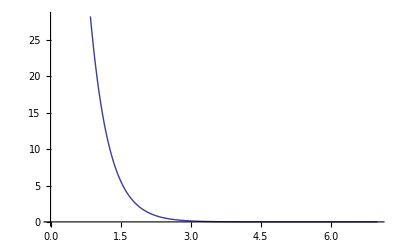

```mathematica
Plot[240/Sqrt[(1+E^(5*(x)))],{x,0,7}]
```

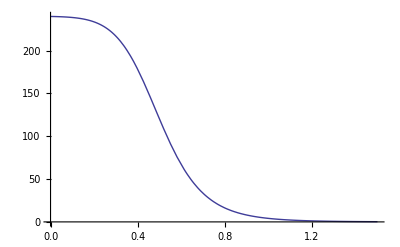

```mathematica
Plot[240/(1+(x+0.5)^10),{x,0,1.5}]
```

```mathematica
dqdt = 4000;
κ=0.142;
T0 =10000;
dT= T0-300;
A = 4Pi;
1/(κ*dT*A/dqdt)
```

0.231095

```mathematica
σ=3*((905.3196)*10^(-9))^2/(2*Pi)
σD=σ*Sqrt[Pi Log[2]]*(1/187)
z=0.01;
dI=0.01;
n=dI/(σ*z)
A=.005*.01;
totn=n*A*z
sum=0.00002*0.65113
forvelocity=100;
IntegratedTotn=sum*A*forvelocity/(σD*z)
```

3.91332×10^-13

3.0881×10^-15

2.55538×10^12

1.27769×10^6

0.0000130226

2.10851×10^9

```mathematica
c/(662.61984*10^(-9))-c/(662.63259*10^(-9))-8.52*10^9
```

1.85499×10^8

```mathematica
1./(250*10^(-9))
```

4.×10^6

```mathematica
Γ=0.95*(3*(905.3196*10^(-9))^3)*{100,600}/(Pi*h*c)
Γt=1/0.003;
```

{3.38863×10^8,2.03318×10^9}

```mathematica
Γ2=43000000;
Γba=100000.;
Fba=Γba/(2*Γ2)
Int=0.05;
Isat=0.25;
A=1;
```

0.00116279

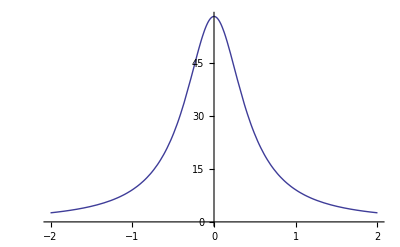

```mathematica
Plot[Fba*(Γba/2)*A*(1/(1+(2*δ*Fba/Γba)^2)),{δ,-200000000,200000000}]
```

```mathematica
1/200000000.
```

5.×10^-9